#### Draw mesh

```mathematica
SetDirectory[NotebookDirectory[]]
(*SetDirectory[FileNameJoin[{ParentDirectory[],"/build-RKDG2D-Desktop-Debug"}]]*)
(*SetDirectory["build-converterUNV-Desktop-u041eu0442u043bu0430u0434u043au0430"]*)
(*SetDirectory[FileNameJoin[{ParentDirectory[],"/build-RKDG2D-Desktop_Qt_5_10_1_MinGW_32bit-Debug"}]]*)
```

/home/v.korchagova/Документы/BMSTU/RKDG2D

```mathematica
mesh=Import["mesh2D","Table"];
```

```mathematica
(*nodes*)
offset=2;
nNodes=mesh[[offset,1]]
nodes=Table[mesh[[i]],{i,offset+1,nNodes+offset}];
(*edges*)
offset=3+nNodes+1+1;
nEdgesBoundary=mesh[[offset,1]]
nEdges=mesh[[offset+1,1]]
edges=Table[mesh[[i]],{i,offset+2,nEdges+offset+1}][[All,2;;]];
(*cells*)
offset = offset +nEdges+4;
nCells=mesh[[offset]][[1]]
cells=Table[mesh[[i]],{i,offset+1,nCells+offset}];
(*adjoint cells for edges*)
offset = nCells+offset+5;
edgeAdj=Table[mesh[[i]],{i,offset,nEdges+offset-3}];

(*edge normals*)
offset = nEdges+offset+2;
edgeNormals=Table[mesh[[i]],{i,offset,nEdges+offset-1}];
```

1089

16

2096

1008

```mathematica
edgeNormals
```

{{-1,0},{-1,0},{-1,0},{-1,0},{1,0},{1,0},{1,0},{1,0},{0,-1.},{0,-1.},{0,-1},{0,-1},{0,-1},{0,-1},{0,-1},{0,-1},{0,-1},{0,-1},{0,-1},{0,-1},{0,1.},{0,1.},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},2032,{1,0},{0,-1},{1,0},{0,-1},{1,0},{2.22045×10^-15,-1},{1,0},{2.22045×10^-15,-1},{1,0},{-6.66134×10^-15,-1},{1,0},{0,-1},{1,0},{4.44089×10^-15,-1},{1,0},{-4.44089×10^-15,-1},{1,0},{0,-1},{0,-1},{0,-1},{0,-1},{0,-1},{2.22045×10^-15,-1},{0,-1},{0,-1},{0,-1},{-2.22045×10^-15,-1},{-2.22045×10^-15,-1},{6.66134×10^-15,-1},{0,-1},{0,-1},{0,-1}}
 |  |  |  |

```mathematica
(*patches*)
offset=offset+nEdges+2;
nPatches=mesh[[offset]][[1]]
offset = offset+1;
patchNames={};
patchEdgeGroups={};
For[i=1,i≤nPatches, ++i,
{
patchNames=Append[patchNames,mesh[[offset,1]]];
(*Print[patchNames];*)
nEdgesInPatch=mesh[[offset+1,1]];
(*Print[nEdgesInPatch];*)
patchEdgeGroups = Append[patchEdgeGroups,Table[mesh[[i,1]],{i,offset+2,offset+1+nEdgesInPatch}]];
offset=offset+2+nEdgesInPatch;
(*Print[offset];*)
}];
patchNames
```

4

{inlet,outlet,walls,step}

```mathematica
(*drawing functions*)
```

```mathematica
drawNode[iNode_]:=Point[nodes[[iNode]]];
drawEdgeArrow[iEdge_]:=Arrow[{nodes[[edges[[iEdge,1]]]],nodes[[edges[[iEdge,2]]]]}];
drawEdgeLine[iEdge_]:=Arrow[{nodes[[edges[[iEdge,1]]]],nodes[[edges[[iEdge,2]]]]}];
drawEdgeNormal[iEdge_]:=Arrow[{(nodes[[edges[[iEdge,1]]]]+nodes[[edges[[iEdge,2]]]])/2,(nodes[[edges[[iEdge,1]]]]+nodes[[edges[[iEdge,2]]]])/2+edgeNormals[[i]]*0.25*Norm[{nodes[[edges[[iEdge,2]]]]-nodes[[edges[[iEdge,1]]]]},2]}];
drawCell[iCell_]:=Polygon[Table[nodes[[cells[[iCell,i]]]],{i,2,cells[[iCell,1]]+1}]];
drawPatch[color_,iPatch_]:={color,Table[drawEdgeLine[patchEdgeGroups[[i,j]]],{j,1,Length[patchEdgeGroups[[i]]]}]};
getCellNodes[iCell_]:=Table[nodes[[cells[[iCell,i]]]],{i,2,cells[[iCell,1]]+1}];
(*areas*)
areas=ParallelTable[Area@drawCell[iCell],{iCell,nCells}];
cellCenters=ParallelTable[{Integrate[x,{x,y}∈drawCell[iCell]],Integrate[y,{x,y}∈drawCell[iCell]]}/areas[[iCell]],{iCell,nCells}];
```

```mathematica
(*pictures*)
```

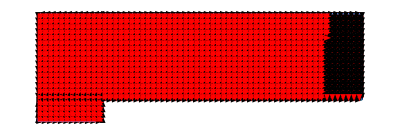

```mathematica
Graphics[{Black,Arrowheads[0.005],
Table[Point[{cellCenters[[i]]}],{i,1,nCells}],
Table[drawEdgeArrow[i],{i,1,nEdges}],
Red,
Table[drawEdgeNormal[i],{i,1,nEdges}],Thick,
Table[drawPatch[RGBColor[i*0.1,i*0.2,i*0.7],i],{i,1,nPatches}]}]
```

```mathematica
Manipulate[Graphics[{EdgeForm[Black],Cyan,
Table[drawCell[i],{i,1,p}],Black,
Table[Point[{cellCenters[[i]]}],{i,1,p}]
},PlotRange->All],{p,1,nCells,1}]
```

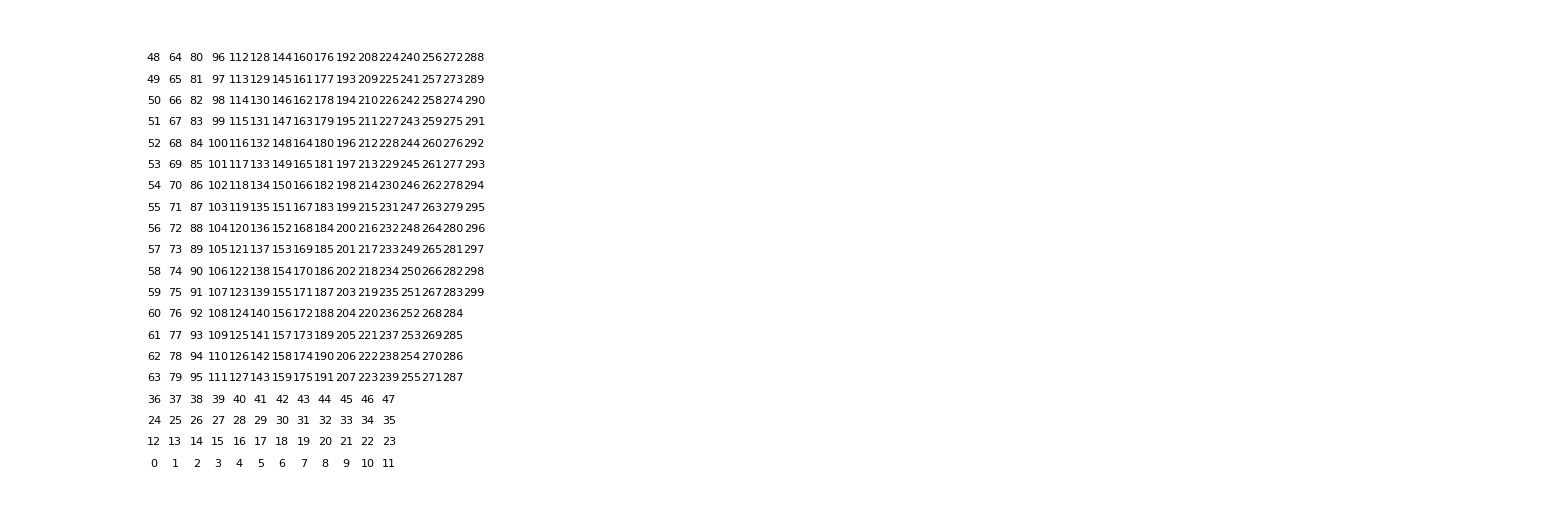

```mathematica
numbers=Graphics[{EdgeForm[Black],Cyan,Opacity[0],
Table[drawCell[i],{i,1,nCells}],Black,Opacity[1],
Table[Text[i-1,cellCenters[[i]]],{i,1,nCells}]
},PlotRange->All]
```

```mathematica
Manipulate[Graphics[{Black,
Table[drawNode[i],{i,{cells[[iCell,2;;2+p]]}}]},PlotRange->Full],{p,0,cells[[iCell,1]]-1,1},{iCell,1,nCells}]
```

#### Basis functions

```mathematica
phi[r_List,iCell_]:={1.0/(√areas[[iCell]]), (r[[1]]-cellCenters[[iCell,1]])/(areas[[iCell]]/(2 √3)),(r[[2]]-cellCenters[[iCell,2]])/(areas[[iCell]]/(2 √3))};
(*phi[r_List,nCell_]:={1.0, r[[1]]-cellCenters[[nCell,1]],r[[2]]-cellCenters[[nCell,2]]};*)
```

```mathematica
gram=Table[Integrate[phi[{x,y},1][[k]]*phi[{x,y},1][[j]],{x,y}∈Polygon[getCellNodes[1]]],{k,3},{j,3}];
gram//MatrixForm
eig=Eigenvalues[gram]
eig[[1]]/eig[[3]]
Det[gram]
```

(1. | -2.77556×10^-16 | 0.
-2.77556×10^-16 | 1. | -2.84217×10^-16
0. | -2.84217×10^-16 | 1.)

{1.,1.,1.}

1.

1.

```mathematica
GetSol[r_List,nCell_,nSol_]:=Sum[alpha[[nCell,nSol,p]]*phi[r,nCell][[p]],{p,1,numFF}]
```

```mathematica
GetSolGraphics[iCell_,nSol_]:=Module[{cNodes},
(cNodes=Table[nodes[[cells[[iCell,i]]]],{i,2,cells[[i,1]]+1}];
Return[Polygon[Table[{cNodes[[i,1]],cNodes[[i,2]],(GetSol[cNodes[[i]],iCell,nSol])},{i,1,cells[[i,1]]}]]]
)]

GetSolGlobal[iCell_,nSol_]:=Module[{cNodes},
(cNodes=Table[nodes[[cells[[iCell,i]]]],{i,2,cells[[i,1]]+1}];
Return[Table[{cNodes[[i,1]],cNodes[[i,2]],GetSol[cNodes[[i]],iCell,nSol]},{i,1,cells[[i,1]]}]]
)]
```

#### Draw solution

```mathematica
(*SetDirectory[FileNameJoin[{ParentDirectory[],"build-RKDG2D-Desktop-u041eu0442u043bu0430u0434u043au0430"}]]*)
SetDirectory[NotebookDirectory[]]
SetDirectory[FileNameJoin[{ParentDirectory[],"build-RKDG2D-Desktop-Debug"}]]
```

C:\Users\vkorchagova\Documents\GitHub\RKDG2D

C:\Users\vkorchagova\Documents\GitHub\build-RKDG2D-Desktop-Debug

```mathematica
coeffs=Import["alphaCoeffs/0.010000","Table"];
numFF=3;
alpha=Table[Partition[coeffs[[i]],numFF],{i,1,nCells}];
```

```mathematica
unstruct=Graphics3D[{Red,ParallelTable[GetSolGraphics[i,1],{i,1,nCells}](*,Blue,Polygon[{{0,0,0},{3,0,0},{3,1,0},{0,1,0}}]*)},AspectRatio->1]
```

-Graphics3D-

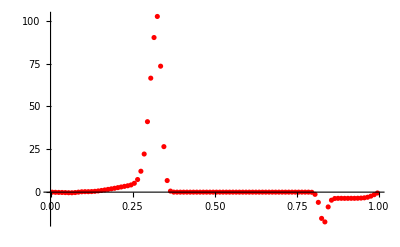

```mathematica
GetSolCenterX[iCell_,nSol_]:={cellCenters[[iCell,1]]+0.5,GetSol[cellCenters[[iCell]],iCell,nSol]};
sol2D=ListPlot[Table[GetSolCenterX[i,2],{i,1,nCells}],PlotRange->All,PlotStyle->Red]
```

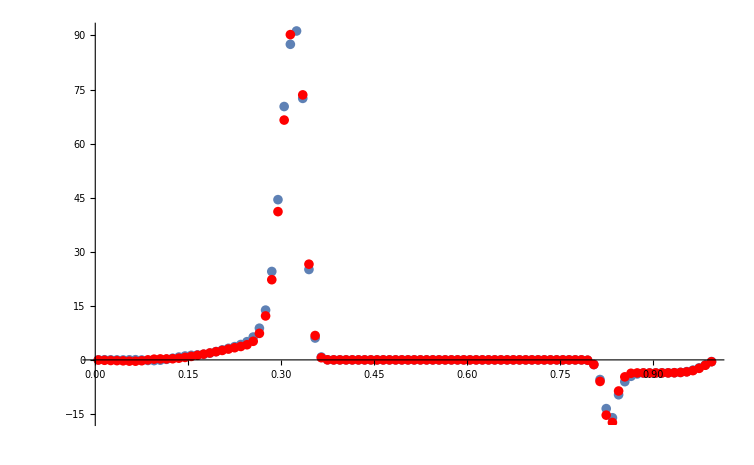

```mathematica
Show[sol1D, sol2D]
```

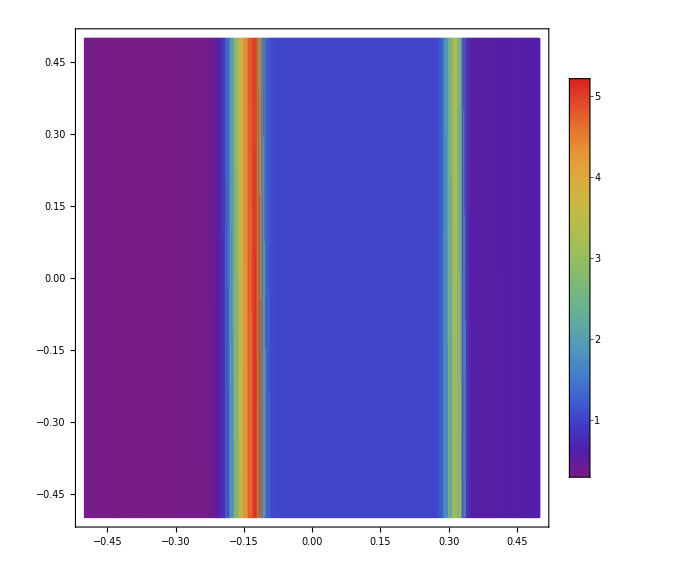

```mathematica
sol=ListDensityPlot[Table[GetSolGlobal[i,1],{i,1,nCells}],PlotRange->All,ColorFunction->"Rainbow",AspectRatio->Automatic,InterpolationOrder->1,PlotLegends->Automatic,BoundaryStyle->Black,ImageSize->Large]
```

#### Troubled cells

```mathematica
trCells=Import["troubledCells.txt","Table"]
colors=Table[Cyan,{i,1,nCells}];
colors[[trCells[[1]]+1]]=Red;
```

Import::nffil: File not found during Import.

$Failed

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Set::pkspec1: The expression 1+$Failed⟦1⟧ cannot be used as a part specification.

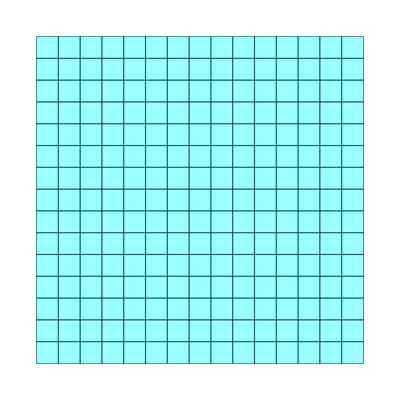

```mathematica
trcells=Graphics[{EdgeForm[Black],Opacity[0.4],
Flatten[Table[{colors[[i]],drawCell[i]},{i,1,nCells}],1]
},PlotRange->All]
```

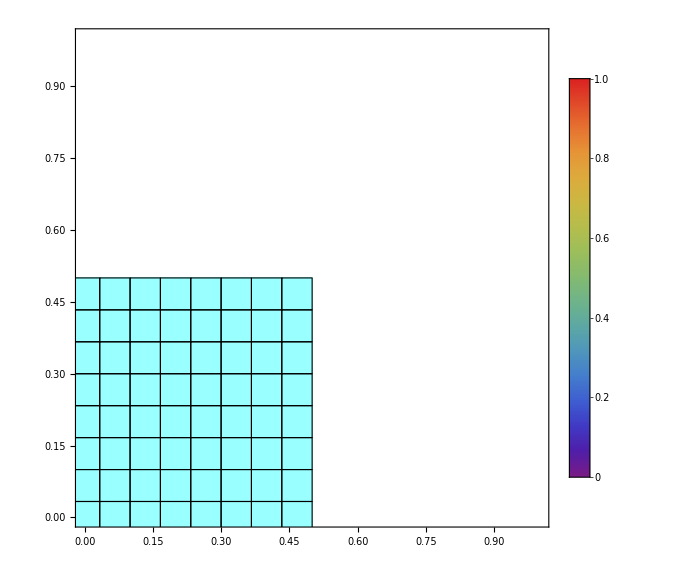

```mathematica
Show[sol,trcells]
```